```mathematica
J=JdJ^(1/2);L=LdL^(1/2); S1=S1dS1^(1/2); S2=S2dS2^(1/2) ;     
Δ1 = ((J^2-L^2-S1^2-S2^2)/2  -   SeffdL/σ2)/(σ1-σ2);
Δ2 = ((J^2-L^2-S1^2-S2^2)/2  -   SeffdL/σ1)/(σ1-σ2);
σ2 = 1+9/(16 (-1+σ1)); 

(*   σ1=(1+3/4 m2/m1);    σ2=(1+3/4  m1/m2);     
Hence, Seff = δ1 S1 + δ2 S2*)  
   
cubic =     L^2 S1^2 S2^2- 2 σ1 σ2 (σ1-σ2)f(f-Δ1)(f-Δ2)-L^2(σ1-σ2)^2 f^2-S2^2 σ2^2(f-Δ1)^2-S1^2 σ1^2(f-Δ2)^2  ;                (*The cubic polynomial of Eq. 3.1 of Cho-Lee*)
cubic=Collect[cubic //Expand//Simplify  ,f]     ;            
cubSol1=((Solve[cubic==0,f])[[1]]);
cubSol2=((Solve[cubic==0,f])[[2]]);
cubSol3=((Solve[cubic==0,f])[[3]]);
f3=f/.cubSol1  ;
f1=f/.cubSol2  ;
f2=f/.cubSol3  ;                      (*The three roots of the cubic*)


(*The following definitions are in Cho-Lee*)
A=  2 σ1 σ2 (σ2-σ1) ;
β=((f2-f1)/(f3-f1))^(1/2);
B1 = 1/2((SeffdL + L^2(σ1+σ2))(J+L)+ L(σ1 S1^2+σ2 S2^2+(σ1+σ2)(Δ2 σ1-Δ1 σ2))) ;
B2 = 1/2((SeffdL + L^2(σ1+σ2))(J-L)- L(σ1 S1^2+σ2 S2^2+(σ1+σ2)(Δ2 σ1-Δ1 σ2))) ;
D1=L(L+J)+Δ2 σ1-Δ1 σ2;
D2=L(L-J)+Δ2 σ1-Δ1 σ2;
B1S = 1/2(-L^2 S1 σ1+J S1^2 σ1-S1^3 σ1-S1 Δ2 σ1^2+J^2 S1 σ2-2 J S1^2 σ2+S1^3 σ2-J Δ1 σ1 σ2+2 S1 Δ1 σ1 σ2+J Δ1 σ2^2-S1 Δ1 σ2^2)  ;
B2S= 1/2(L^2 S1 σ1+J S1^2 σ1+S1^3 σ1+S1 Δ2 σ1^2-J^2 S1 σ2-2 J S1^2 σ2-S1^3 σ2-J Δ1 σ1 σ2-2 S1 Δ1 σ1 σ2+J Δ1 σ2^2+S1 Δ1 σ2^2)   ;
D1S=-J S1+S1^2-Δ1 σ2;
D2S=(J S1+S1^2-Δ1 σ2);
α1 = ((σ1-σ2)(f2-f1))/(D1-f1(σ1-σ2))  ;
α2 = ((σ1-σ2)(f2-f1))/(D2-f1(σ1-σ2))  ;
α1S = ((-σ1)(f2-f1))/(D1S+f1 σ1)  ;
α2S = ((-σ1)(f2-f1))/(D2S+f1 σ1)  ;

B1S2 =  (-J^2 S2 σ1+2 J S2^2 σ1-S2^3 σ1+J Δ2 σ1^2-S2 Δ2 σ1^2+L^2 S2 σ2-J S2^2 σ2+S2^3 σ2-J Δ2 σ1 σ2+2 S2 Δ2 σ1 σ2-S2 Δ1 σ2^2)/2 ;
B2S2=(J^2 S2 σ1+2 J S2^2 σ1+S2^3 σ1+J Δ2 σ1^2+S2 Δ2 σ1^2-L^2 S2 σ2-J S2^2 σ2-S2^3 σ2-J Δ2 σ1 σ2-2 S2 Δ2 σ1 σ2+S2 Δ1 σ2^2)/2  ;
D1S2= (J S2-S2^2-Δ2 σ1+0f σ2);
D2S2= (-J S2-S2^2-Δ2 σ1+0f σ2);
α1S2 = ((-σ2)(f2-f1))/(D1S2+f1 σ2)  ;
α2S2 = ((-σ2)(f2-f1))/(D2S2+f1 σ2)  ;


Clear[J,L,S1,S2];
```

```mathematica
R  ={Rx, Ry, Rz};                        P  ={Px, Py, Pz};
S1={S1x,S1y,S1z};                   S2={S2x,S2y,S2z};
S=S1+S2;
PdR =P.R;               RdR=R.R;            PdP=P.P;
RdS1=R.S1;           PdS1=P.S1;        RdS2=R.S2;           PdS2=P.S2;

(*  The phase space variables are R, P, R1, P1, R2, P2. Now, we compute their Poisson brackets with the commuting constants 
J^2, L^2, Seff.L, S1^2, S2^2.
Notation:    RpbJdJ := {R_vector , JdJ}  ; JdJ = J.J    *)
RpbJdJ:= 2 RdR P[[i]]-2 (PdR R[[i]]+Cross[R,S][[i]])    ;  
PpbJdJ:= 2 PdR P[[i]]-2 (PdP R[[i]]+Cross[P,S][[i]])    ;   
S1pbJdJ:=2 RdS1 P[[i]]-2 (PdS1 R[[i]]+Cross[S1,S2][[i]]);
S2pbJdJ:= 2 (RdS2 P[[i]]-PdS2 R[[i]]+Cross[S1,S2][[i]]);
RpbLdL:=2 RdR P[[i]]-2 PdR R[[i]]   ;  
PpbLdL:=2 PdR P[[i]]-2 PdP R[[i]]   ;   
S1pbLdL:=0;
S2pbLdL:=0;
RpbSeffdL:= -Cross[R,σ1 S1+σ2 S2][[i]]  ;                      
PpbSeffdL:=   -Cross[P,σ1 S1+σ2 S2][[i]];  
S1pbSeffdL:=σ1(RdS1 P[[i]]-PdS1 R[[i]]);
S2pbSeffdL:=σ2(RdS2 P[[i]]-PdS2 R[[i]]);

CCVec={SeffdL,JdJ, LdL,S1dS1,S2dS2};                           (*vector (column) of commuting constants (CCs) *)
VpbC = ConstantArray[0,{12, Length[CCVec]}];

(*
Now we will put the Poisson bracket of all the phase space variables wrt. all the commuting constants in a 18x5 matrix
Rows (columns) correspond to phase space variables (commuting constants). 
Inspiration for naming VpbC : V -> phase space variable; pb -> Poisson bracket; C -> (commuting)constants
*)
Do[
VpbC[[i,2]]       =RpbJdJ;
VpbC[[3+i,2]] =PpbJdJ;
VpbC[[6+i,2]] =S1pbJdJ;
VpbC[[9+i,2]] =S2pbJdJ;
,{i,1,3}];
Do[
VpbC[[i,3]]       =RpbLdL;
VpbC[[3+i,3]] =PpbLdL;
VpbC[[6+i,3]] =S1pbLdL;
VpbC[[9+i,3]] =S2pbLdL;
,{i,1,3}];
Do[
VpbC[[i,1]]       =RpbSeffdL;
VpbC[[3+i,1]] =PpbSeffdL;
VpbC[[6+i,1]] =S1pbSeffdL;
VpbC[[9+i,1]] =S2pbSeffdL;
,{i,1,3}];
Do[VpbC[[i,j]]=0;
{i,1,12},{j,4,5} ];
VpbC = VpbC   //Simplify   ;
```

Set::pkspec1: The expression i cannot be used as a part specification.

```mathematica
(*Δλs are the flow amount along each commuting constant (one at a time) required to close a loop in the EPS picture*)

ΔΥ=   EllipticK[β^2]  ;
Δλ1= (4ΔΥ)/(A(f3-f1))^(1/2);
Δλ2=(-1/(2 JdJ^(1/2))) (4/(A(f3-f1))^(1/2)) ((B1  EllipticPi[α1,β^2])/(D1-f1(σ1-σ2))+(B2 EllipticPi[α2,β^2])/(D2-f1(σ1-σ2)))      ;
Δλ3=(-1/(2 LdL^(1/2)))( (4/(A(f3-f1))^(1/2)) ((B1  EllipticPi[α1,β^2])/(D1-f1(σ1-σ2))-(B2 EllipticPi[α2,β^2])/(D2-f1(σ1-σ2)))  - (SeffdL +(Δ1-Δ2)σ1 σ2 + LdL(σ1+σ2))Δλ1/LdL^(1/2) )  ;
Δλ4=(-1/(2 S1dS1^(1/2)))((4/(A(f3-f1))^(1/2))(-(B1S EllipticPi[α1S,β^2])/(D1S+f1 σ1)+(B2S EllipticPi[α2S,β^2])/(D2S+f1 σ1))  +  S1dS1^(1/2)(σ2-σ1)Δλ1  )  ;
Δλ5=(-1/(2 S2dS2^(1/2)))((4/(A(f3-f1))^(1/2))(-(B1S2 EllipticPi[α1S2,β^2])/(D1S2+f1 σ2)+(B2S2 EllipticPi[α2S2,β^2])/(D2S2+f1 σ2))  +  S2dS2^(1/2)(σ1-σ2)Δλ1  )  ;
ΔλVec = {Δλ1,Δλ2,Δλ3,Δλ4,Δλ5};

(*This is the Jacobian matrix (∂ Subscript[Δλ, i])/∂ Subscript[CC, j]                     
Subscript[Δλ, i] := ith flow amount;    Subscript[CC, j]:= jth commuting constant.
We will use this later*)
dΔλdCC = ConstantArray[0,{Length[ΔλVec],Length[CCVec]}] ;
Do[dΔλdCC[[i,j]] = D[ΔλVec[[i]],CCVec[[j]]]
,{i,1,Length[ΔλVec]},{j,1,Length[CCVec]}]
```

```mathematica
(*This is the initial data for the phase space variables*)
σ1=1.5;
varRinit={1, 5, -3}//N;                 varPinit={5, -2, 3}//N;
varR1init={2, 1, 1}//N;                                         varP1init={1, -1, -3}//N;
varR2init={-1, -1/2, 1/2}//N;                        varP2init={2, -2, -1}//N;
varS1init=Cross[varR1init,varP1init];          varS2init=Cross[varR2init,varP2init];

S1dS1=Norm[Cross[varR1init,varP1init]]^2;          S2dS2=Norm[Cross[varR2init,varP2init]]^2;                          LdL=Norm[Cross[varRinit,varPinit]]^2;
SeffdL=(σ1 Cross[varR1init,varP1init]+σ2 Cross[varR2init,varP2init]).Cross[varRinit,varPinit];
JdJ= Norm[(Cross[varRinit,varPinit]+Cross[varR1init,varP1init]+Cross[varR2init,varP2init])]^2;
dΔλdCCNum= dΔλdCC //Re;                       (*This is the Jacobian matrix (∂ Subscript[Δλ, i])/∂ Subscript[CC, j] *)
ΔλVecNum =ΔλVec //Re;                           (*Column of flow amounts along the commuting constants*)
```

```mathematica
(*
Let V be the vector of all 12 phase space variables R, P, S1, S2. Let Subscript[C, i]:=ith commuting constant. Now,  
 {V, J5} = {V, Subscript[C, i] Δλ^i/π} ={V, Subscript[C, i] Δλ^i}/π
= {V,Subscript[C, i]} Δλ^i + {V,Subscript[C, j]} ((∂ Subscript[Δλ, i])/∂ Subscript[CC, j]) Subscript[C, i]               (*can be proved with 2 lines of algebra using the theorem {f,g(Subscript[x, i])} = {f,Subscript[x, i]} (∂g/∂x^i)   *)
= (VpbC.ΔλVecNum + VpbC.Transpose[dΔλdCCNum].CCVec )/(1.π)           (*in Mathematica code form*) 
*)

GrandMatrix = (VpbC.ΔλVecNum + VpbC.Transpose[dΔλdCCNum].CCVec)/(1.π) //Simplify ;                     (*This is {V, J5}. How? See the comment just above*)
SubsList1={Rx->Rx[t],Ry->Ry[t],Rz->Rz[t],Px->Px[t],Py->Py[t],Pz->Pz[t],S1x->S1x[t],S1y->S1y[t],S1z->S1z[t],S2x->S2x[t],S2y->S2y[t],S2z->S2z[t]} ;
V1=Join[R,P,S1,S2]  ;
V2=V1/.SubsList1;
V3=D[V1/.SubsList1,t];
V4=V2/.t->0;
Vinit=Join[varRinit,varPinit,varS1init,varS2init];                 (*Initial data vector*)
VpbCRHS= (    GrandMatrix  /.SubsList1  //Simplify)   ;                    (*This column matrix stores {Subscript[V, i], J5} with Subscript[V, i] = ith phase space variable *)
```

```mathematica
V1oft=#[t]&/@V1;
```

-1.69874+4.01428 x

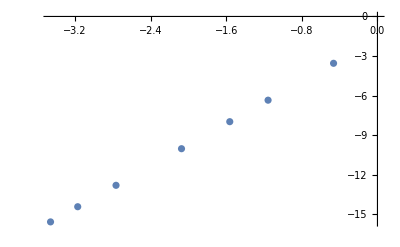

```mathematica
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];

tInit=0.;   tFin=   2π ;                                        (*Let the flow amount be 2 π*)
dtArray = (tFin-tInit){1/10,1/20,1/30,1/50,1/100,1/150,1/200};
errorArr=0dtArray;

Do[
sol1=NDSolve[{    V3==VpbCRHS,    V4==Vinit  },V1,{t,tInit,tFin} , StartingStepSize->dtArray[[i]],Method->{"FixedStep",Method->{"ExplicitRungeKutta","DifferenceOrder"->4(*,"StiffnessTest"->False*)}}  ] ;                   (*We flow along J5*)               
StepDataPlot[sol1];

RxFn[x_]:=(Rx/.sol1[[1]][[1]])[x];                RyFn[x_]:=(Ry/.sol1[[1]][[2]])[x];              RzFn[x_]:=(Rz/.sol1[[1]][[3]])[x];
PxFn[x_]:=(Px/.sol1[[1]][[4]])[x];                PyFn[x_]:=(Py/.sol1[[1]][[5]])[x];              PzFn[x_]:=(Pz/.sol1[[1]][[6]])[x];
S1xFn[x_]:=(S1x/.sol1[[1]][[7]])[x];           S1yFn[x_]:=(S1y/.sol1[[1]][[8]])[x];          S1zFn[x_]:=(S1z/.sol1[[1]][[9]])[x];
S2xFn[x_]:=(S2x/.sol1[[1]][[10]])[x];         S2yFn[x_]:=(S2y/.sol1[[1]][[11]])[x];        S2zFn[x_]:=(S2z/.sol1[[1]][[12]])[x];
RFn[x_]:={RxFn[x],RyFn[x],RzFn[x]};             PFn[x_]:={PxFn[x],PyFn[x],PzFn[x]};
S1Fn[x_]:={S1xFn[x],S1yFn[x],S1zFn[x]};    S2Fn[x_]:={S2xFn[x],S2yFn[x],S2zFn[x]};     

error=(V1oft/.t->tFin)-(V1oft/.t->tInit)/.sol1;
errorArr[[i]]=Norm[error];
,{i,1,Length@dtArray}]


Fit[Log[Transpose[{dtArray,errorArr}]    ],{1,x},x]
ListPlot[  Log[Transpose[{dtArray,errorArr}]    ]   ]                          (*the slope of log(error) vs log(dt) *)
```

```mathematica
(*Slope is ~5 for 4th and 5th order RK4. For 4th order, it should be ~4*)
```